# Code for generating Fig 2 (both panels, DFT as external input)

### Initializing global parameters:

```mathematica
Xmin=-10;                                    (* Lower limit range for the function *)
Xmax=10;                                      (* Upper limit range for the function *)
dx=0.025;                                       (*Step size for the finite element method*)
x=Range[Xmin,Xmax,dx]; (*Initialize the abcissa*)
len=Length[x];     (*Initialize the lengeth of solution vector*)

(*Laplacian matrix for the discrete system*)
lap=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{len,len}]/dx^2;
```

### Variable initialization:

#### Placeholders for solving the differential equation `exactly’

```mathematica
phi=Array[phiVal,len];(* Placeholder for a particular eigenfunction we are calculating *)
psi=Array[phiVal,len];(* Placeholder for a particular dual function we are calculating *)
lam;(* Placeholder for a particular eigenvalue we are calculating *)
```

### Eigenvalue Problem definition:

We are interested in solving for the stationary states of the Gross-Pitaevskii equation in 1 dimension with a harmonic potential:

```mathematica
q0=10; (*Nonlinear coupling for the Gross–Pitaevskii equation*)
k0=0.5;      (*Coupling constant for the harmonic potential*)

eigEq[q_,k_]:=(Dot[-lap,phi]+k*(x^2)*phi+q*phi^3==lam*phi);(*Eigenvalue equation*)
normEq[q_,k_]:=Dot[phi,phi]==1.0/dx;(*Normalization condition*)

eqns[q_,k_]:=Append[Thread[eigEq[q,k]],normEq[q,k]]; (*Full (n+1) equation set*)
```

### Example for finding the lowest energy solution:

We utilize FindRoot to find the solution to the eigenvalue equation. We use an eigenfunction of the harmonic oscillator, or a constant function, as an initial guess to speed up calculations. FindRoot allows us to bypass finding all of the other eigenfunctions we don’t care about by starting near the basin of attraction of the first eigenmode.

```mathematica
guess0=Exp[-x^2/2]/(Pi)^(1/4);
guess02=Exp[-x^2/1.5]/(Pi)^(1/4);
```

```mathematica
guess=Exp[-x^2/2]/(Pi)^(1/4); (*Harmonic oscillator eigenfunction guess*)
sol2=FindRoot[eqns[q0,k0],Transpose[{Prepend[phi,lam],Prepend[guess,1]}],PrecisionGoal->20]; (*Solution routine for the full set of (n+1) equations*)
lam/.sol2 (*Sanity check station: We can check lambda for q=0 to verify we get the harmonic oscillator eigenvalue*)
```

3.1645

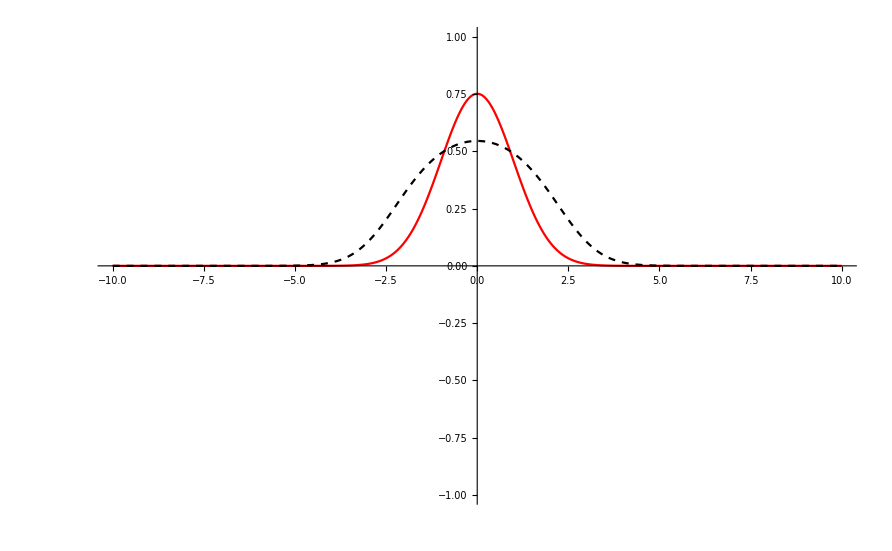

```mathematica
Show[ListLinePlot[Transpose[{x,Exp[-x^2/2]/(Pi)^(1/4)}],PlotRange->{{-10,10},{-1,1}},PlotStyle->Red],
ListPlot[Transpose[{x,Flatten[phi/.sol2]}],PlotRange->{{-10,10},{-1,1}},PlotStyle->{Dashed,Black},Joined->True]]
```

### Manipulate to observe the solutions

```mathematica
sol[q_,k_]:=FindRoot[eqns[q,k],Transpose[{Prepend[phi,lam],Prepend[Exp[-x^2*Sqrt[k]/2]/(Pi/Sqrt[k])^(1/4),Sqrt[k]]}],PrecisionGoal->20]; (*Solution routine for the full set of (n+1) equations, as a function of a and/or k*)
```

```mathematica
solGuess[q_,k_,Guess_]:=FindRoot[eqns[q,k],Transpose[{Prepend[phi,lam],Flatten[Guess]}],PrecisionGoal->20];
```

```mathematica
(*Guess should be of the form {lam guess, phi guess}*)
```

```mathematica
Manipulate[Show[ListLinePlot[Transpose[{x,Flatten[phi/.sol[q,k]]}],PlotRange->{{-10,10},{-.1,1}},PlotStyle->{Black},InterpolationOrder->2],
ListLinePlot[Transpose[{x,Exp[-x^2/2]/(Pi)^(1/4)}],PlotRange->{{-5,5},{-.1,1}},PlotStyle->Red]]
,{q,-3,10},{k,1,10}] (*NOTE: The root algorithm does not always converge to the smallest eigenfunction for large or negative a, I need a fast method to find the eigenpair that reliable converges to the first root*)
```

```mathematica
TrainingPoints={{0,1},{0,5},{5/10.0,1},{5/10.0,5}};(*{q,k}*)
numTrain=Length[TrainingPoints]; (*Number of training points*)
```

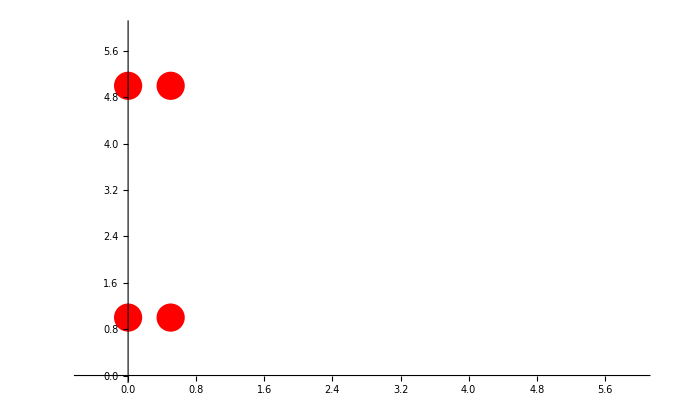

```mathematica
ListPlot[TrainingPoints,PlotStyle->{PointSize[0.03],Red},PlotRange->{{-0.5,6},{0,6}}]
```

```mathematica
klist={0.5,2,4,10,30};
```

```mathematica
(*TestingPoints=Join[Table[{i,klist[[j]]},{i,-100,-0.1,5},{j,1,Length[klist]}],Table[{i,klist[[j]]},{i,0,6,2},{j,1,Length[klist]}],Table[{i,klist[[j]]},{i,10,100,10},{j,1,Length[klist]}]];*)
```

```mathematica
TestingPointsPlus=Table[{i,klist[[j]]},{i,0,10,2},{j,1,Length[klist]}];
TestingPointsNeg=Table[{i,klist[[j]]},{i,0,-10,-2},{j,1,Length[klist]}];
```

```mathematica
Results={};
```

```mathematica
listPhi=Array[trainPhi,{numTrain,len}]; (*List of the training functions 'phi'*)
listPsi=Array[trainPsi,{numTrain,len}];(*List of the training dual functions 'psi'*)
listCoeff=Array[aTest,numTrain];(*Coefficients of the Galerkin approximated solution*)
```

```mathematica
For[i=1,i≤numTrain,i++,
listPhi[[i]]=phi/.sol[TrainingPoints[[i]][[1]],TrainingPoints[[i]][[2]]];
listPsi[[i]]=listPhi[[i]](*psi=phi for the first flavor of the galerkin method*)
]
```

```mathematica
(*For[i=1,i<=Length[TestingPoints],i++,
Print[i];
ResultsForiFixed={};

For[j=1,j<=Length[TestingPoints[[i]]], j++,



testpoint=TestingPoints[[i]][[j]]; (*Test Value of a, for sanity checks and to test the resuls of our scheme*)
testPhi=Dot[Transpose[listPhi],listCoeff]; (*Definition for the test function Phi*)

eigGaler={};

For[ij=1,ij≤numTrain,ij++,
AppendTo[eigGaler,
Dot[listPsi[[ij]],Dot[-lap,testPhi]+testpoint[[2]]*(x^2)*testPhi+testpoint[[1]]*testPhi^3]==Dot[listPsi[[ij]],lam2*testPhi]


]];
normGaler=Dot[testPhi,testPhi]==1;
eqnsGaler=Append[eigGaler,normGaler];(*Full equation set*)



guess2=ConstantArray[0.1,numTrain]; (*eigenfunction guess*)
solGaler=FindRoot[eqnsGaler,Transpose[{Prepend[listCoeff,lam2],Prepend[guess2,1]}],PrecisionGoal->20]; (*Solution routine for the full set of equations*)



AppendTo[ResultsForiFixed,{TestingPoints[[i]][[j]],solGaler}]



];
AppendTo[Results,ResultsForiFixed];




]*)
```

```mathematica
(*For[KIndex=1,KIndex<=Length[TestingPoints[[1]]],KIndex++,*)
For[KIndex=1,KIndex≤Length[TestingPointsPlus[[1]]],KIndex++,
Print[KIndex];
ResultsForKIndexFixedPlus={};

Guess=Join[{Sqrt[TestingPointsPlus[[1]][[KIndex]][[2]]]},ConstantArray[0.1,numTrain]]; (*eigenfunction guess*)


(*Loop for positive qs*)
For[QIndex=1,QIndex≤Length[TestingPointsPlus], QIndex++,


testpoint=TestingPointsPlus[[QIndex]][[KIndex]]; (*Test Value of a, for sanity checks and to test the resuls of our scheme*)
testPhi=Dot[Transpose[listPhi],listCoeff]; (*Definition for the test function Phi*)

eigGaler={};

For[ij=1,ij≤numTrain,ij++,
AppendTo[eigGaler,
Dot[listPsi[[ij]],Dot[-lap,testPhi]+testpoint[[2]]*(x^2)*testPhi+testpoint[[1]]*testPhi^3]==Dot[listPsi[[ij]],lam2*testPhi]


]];
normGaler=Dot[testPhi,testPhi]==1.0/dx;
eqnsGaler=Append[eigGaler,normGaler];(*Full equation set*)




solGaler=FindRoot[eqnsGaler,Transpose[{Prepend[listCoeff,lam2],Guess}],PrecisionGoal->20]; (*Solution routine for the full set of equations*)
Guess=Flatten[{lam2,listCoeff}/.solGaler];
If[QIndex==1,
Guess0=Guess
];


AppendTo[ResultsForKIndexFixedPlus,{TestingPointsPlus[[QIndex]][[KIndex]],solGaler}]



];

(*Loop for negative qs*)
Guess=Guess0;
ResultsForKIndexFixedNeg={};
For[QIndex=1,QIndex≤Length[TestingPointsNeg], QIndex++,


testpoint=TestingPointsNeg[[QIndex]][[KIndex]]; (*Test Value of a, for sanity checks and to test the resuls of our scheme*)
testPhi=Dot[Transpose[listPhi],listCoeff]; (*Definition for the test function Phi*)

eigGaler={};

For[ij=1,ij≤numTrain,ij++,
AppendTo[eigGaler,
Dot[listPsi[[ij]],Dot[-lap,testPhi]+testpoint[[2]]*(x^2)*testPhi+testpoint[[1]]*testPhi^3]==Dot[listPsi[[ij]],lam2*testPhi]


]];
normGaler=Dot[testPhi,testPhi]==1.0/dx;
eqnsGaler=Append[eigGaler,normGaler];(*Full equation set*)




solGaler=FindRoot[eqnsGaler,Transpose[{Prepend[listCoeff,lam2],Guess}],PrecisionGoal->20]; (*Solution routine for the full set of equations*)
Guess=Flatten[{lam2,listCoeff}/.solGaler];



AppendTo[ResultsForKIndexFixedNeg,{TestingPointsNeg[[QIndex]][[KIndex]],solGaler}]



];





AppendTo[Results,Join[Reverse[ResultsForKIndexFixedNeg],ResultsForKIndexFixedPlus]];




]
```

1

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

2

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

3

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

4

5

```mathematica
TestPointJointList=Join[Reverse[TestingPointsNeg],TestingPointsPlus]
```

{{{-10,0.5},{-10,2},{-10,4},{-10,10},{-10,30}},{{-8,0.5},{-8,2},{-8,4},{-8,10},{-8,30}},{{-6,0.5},{-6,2},{-6,4},{-6,10},{-6,30}},{{-4,0.5},{-4,2},{-4,4},{-4,10},{-4,30}},{{-2,0.5},{-2,2},{-2,4},{-2,10},{-2,30}},{{0,0.5},{0,2},{0,4},{0,10},{0,30}},{{0,0.5},{0,2},{0,4},{0,10},{0,30}},{{2,0.5},{2,2},{2,4},{2,10},{2,30}},{{4,0.5},{4,2},{4,4},{4,10},{4,30}},{{6,0.5},{6,2},{6,4},{6,10},{6,30}},{{8,0.5},{8,2},{8,4},{8,10},{8,30}},{{10,0.5},{10,2},{10,4},{10,10},{10,30}}}

```mathematica
TrueLambdasPointsPlus=Table[TestingPointsPlus[[i]][[j]],{i,1,Length[TestingPointsPlus]},{j,1,Length[TestingPointsPlus[[1]]]}]
```

{{{0,0.5},{0,2},{0,4},{0,10},{0,30}},{{2,0.5},{2,2},{2,4},{2,10},{2,30}},{{4,0.5},{4,2},{4,4},{4,10},{4,30}},{{6,0.5},{6,2},{6,4},{6,10},{6,30}},{{8,0.5},{8,2},{8,4},{8,10},{8,30}},{{10,0.5},{10,2},{10,4},{10,10},{10,30}}}

```mathematica
TrueLambdasPointsNeg=Table[TestingPointsNeg[[i]][[j]],{i,1,Length[TestingPointsNeg]},{j,1,Length[TestingPointsNeg[[1]]]}]
```

{{{0,0.5},{0,2},{0,4},{0,10},{0,30}},{{-2,0.5},{-2,2},{-2,4},{-2,10},{-2,30}},{{-4,0.5},{-4,2},{-4,4},{-4,10},{-4,30}},{{-6,0.5},{-6,2},{-6,4},{-6,10},{-6,30}},{{-8,0.5},{-8,2},{-8,4},{-8,10},{-8,30}},{{-10,0.5},{-10,2},{-10,4},{-10,10},{-10,30}}}

```mathematica
TrueLambdas={};
```

```mathematica
TrueWF={};
```

```mathematica
For[KIndex=1,KIndex≤Length[TrueLambdasPointsPlus[[1]]],KIndex++,
TrueLambdasFixedKIndexPlus={};
TrueWFFixedKIndexPlus={};
(*Guess={lam,phi}/.sol[TrueLambdasPointsPlus[[1]][[KIndex]][[1]],TrueLambdasPointsPlus[[1]][[KIndex]][[2]]];*)
Guess={Sqrt[TrueLambdasPointsPlus[[1]][[KIndex]][[2]]],guess0};
(*AppendTo[TrueLambdasFixedKIndexPlus,{TrueLambdasPointsPlus[[11]][[KIndex]],Guess[[1]]}];*)
(*For[QIndex=1,QIndex<=Length[TrueLambdasPointsPlus],QIndex++,*)
For[QIndex=1,QIndex≤Length[TrueLambdasPointsPlus],QIndex++,
Guess={lam,phi}/.solGuess[TrueLambdasPointsPlus[[QIndex]][[KIndex]][[1]],TrueLambdasPointsPlus[[QIndex]][[KIndex]][[2]],Guess];
If[QIndex==1,
Guess0=Guess];
AppendTo[TrueLambdasFixedKIndexPlus,{{TrueLambdasPointsPlus[[QIndex]][[KIndex]][[1]],TrueLambdasPointsPlus[[QIndex]][[KIndex]][[2]]},Guess[[1]]}];

AppendTo[TrueWFFixedKIndexPlus,{{TrueLambdasPointsPlus[[QIndex]][[KIndex]][[1]],TrueLambdasPointsPlus[[QIndex]][[KIndex]][[2]]},Guess[[2]]}];

];
TrueLambdasFixedKIndexNeg={};
TrueWFFixedKIndexNeg={};
Guess=Guess0;
For[QIndex=1,QIndex<=Length[TrueLambdasPointsNeg],QIndex++,
Guess={lam,phi}/.solGuess[TrueLambdasPointsNeg[[QIndex]][[KIndex]][[1]],TrueLambdasPointsNeg[[QIndex]][[KIndex]][[2]],Guess];
AppendTo[TrueLambdasFixedKIndexNeg,{{TrueLambdasPointsNeg[[QIndex]][[KIndex]][[1]],TrueLambdasPointsNeg[[QIndex]][[KIndex]][[2]]},Guess[[1]]}];

AppendTo[TrueWFFixedKIndexNeg,{{TrueLambdasPointsNeg[[QIndex]][[KIndex]][[1]],TrueLambdasPointsNeg[[QIndex]][[KIndex]][[2]]},Guess[[2]]}];

];






AppendTo[TrueLambdas,Join[Reverse[TrueLambdasFixedKIndexNeg],   TrueLambdasFixedKIndexPlus    ]    ];
AppendTo[TrueWF,Join[Reverse[TrueWFFixedKIndexNeg] ,TrueWFFixedKIndexPlus  ]   ]

(*AppendTo[TrueLambdas,TrueLambdasFixedKIndexPlus       ];*)
]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

General::munfl: (3.4801×10^-115)^3 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.34659×10^-114)^3 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (4.84985×10^-114)^3 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
GuessLambdas=Table[{TestPointJointList[[i]][[j]], lam2/.Results[[j]][[i]][[2]][[1]] },{i,1,Length[TestPointJointList]},{j,1,Length[TestPointJointList[[1]]]}];
```

```mathematica
GuessLamsPlot=Table[{GuessLambdas[[i]][[j]][[1]][[1]],GuessLambdas[[i]][[j]][[2]]},{j,1,Length[GuessLambdas[[1]]]},{i,1,Length[GuessLambdas]}];
```

```mathematica
TrueLamsPlot=Table[{TrueLambdas[[i]][[j]][[1]][[1]],TrueLambdas[[i]][[j]][[2]]},{i,1,Length[TrueLambdas]},{j,1,Length[TrueLambdas[[1]]]}]
```

{{{-10,-6.31013},{-8,-4.07266},{-6,-2.32439},{-4,-1.01465},{-2,-0.0427646},{0,0.707087},{0,0.707087},{2,1.32139},{4,1.85129},{6,2.32528},{8,2.7597},{10,3.1645}},{{-10,-6.40605},{-8,-4.14264},{-6,-2.30684},{-4,-0.824437},{-2,0.390383},{0,1.41414},{0,1.41414},{2,2.30385},{4,3.09822},{6,3.82271},{8,4.49422},{10,5.1242}},{{-10,-6.46282},{-8,-4.14313},{-6,-2.20721},{-4,-0.584025},{-2,0.79799},{0,1.99984},{0,1.99984},{2,3.06809},{4,4.03619},{6,4.92767},{8,5.75909},{10,6.54231}},{{-10,-6.47448},{-8,-4.00555},{-6,-1.86325},{-4,0.0109996},{-2,1.67098},{0,3.16189},{0,3.16189},{2,4.51955},{4,5.77142},{6,6.93827},{8,8.03576},{10,9.07576}},{{-10,-6.15495},{-8,-3.36659},{-6,-0.848948},{-4,1.44006},{-2,3.53778},{0,5.47605},{0,5.47605},{2,7.28128},{4,8.975},{6,10.5746},{8,12.0942},{10,13.545}}}

```mathematica
TrainingPoints
```

{{0,1},{0,5},{0.5,1},{0.5,5}}

```mathematica
lam/.sol[TrainingPoints[[1]][[1]],TrainingPoints[[1]][[2]]]
```

0.999961

```mathematica
TrainingLocations=Table[{TrainingPoints[[i]][[1]],


lam/.sol[TrainingPoints[[i]][[1]],TrainingPoints[[i]][[2]]]
},{i,1,4}]
```

{{0,0.999961},{0,2.23587},{0.5,1.19544},{0.5,2.53013}}

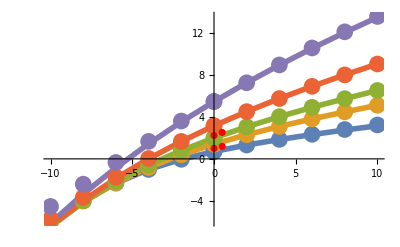

```mathematica
pt=Show[ListPlot[GuessLamsPlot,PlotStyle->{PointSize[0.01]}],ListPlot[TrueLamsPlot,Joined->True,PlotStyle->{Thickness[0.01]}],ListPlot[GuessLamsPlot,PlotStyle->{PointSize[0.03]}],ListPlot[TrainingLocations,PlotStyle->Red]]
```

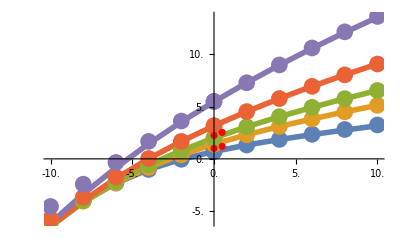

```mathematica
c=3;
tx=Map[MapAt[c #&,#,3]&,Ticks/.AbsoluteOptions[pt,Ticks],{2}];
Show[pt,Ticks->tx]
```

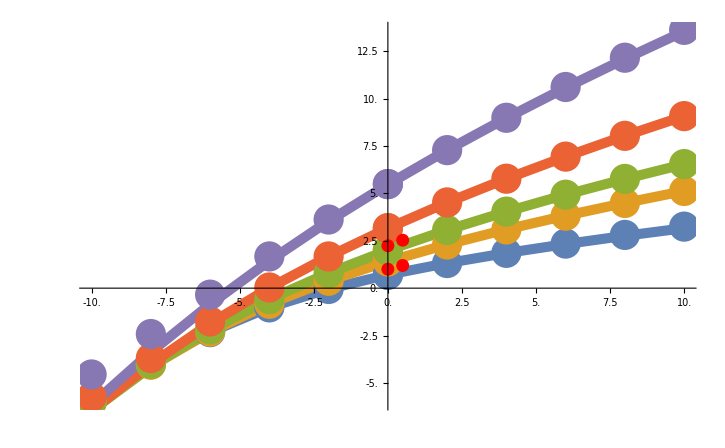

```mathematica
Show[%,PlotLabel->None,LabelStyle->{FontFamily->"cmr10",50,GrayLevel[0]}]
```

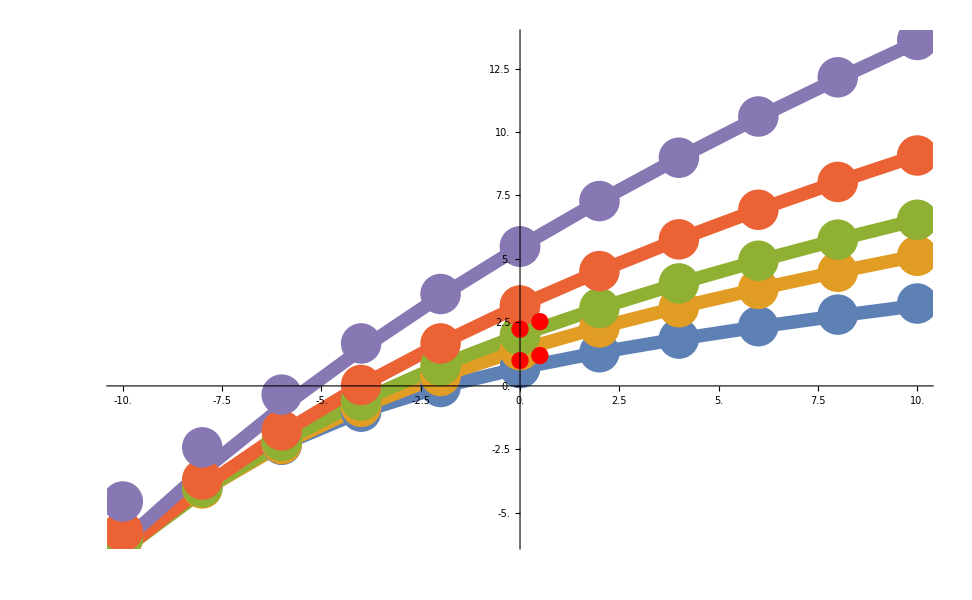

```mathematica
Show[%,AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[3]],Method->{"CoordinatesToolOptions"->{"DisplayFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&),"CopiedValueFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&)}}]
```

```mathematica
HF1={{30,0.186611182251415},{45,0.194899338168498},{60,0.203740143627412},{75,0.213225879641686},{90,0.22345839555028},{105,0.234550797257512},{120,0.246628872033028},{135,0.259832720266737},{150,0.274318196233815},{165,0.290258223792226},{180,0.307844256079146},{195,0.327287593401953}};
HF2={{30,0.184361830817538},{45,0.190482016056611},{60,0.19687203559579},{75,0.203575059945187},{90,0.210636342644662},{105,0.218103622228673},{120,0.226027482629331},{135,0.23446167329442},{150,0.243463385164449},{165,0.253093483988122},{180,0.263416713062385},{195,0.274501849884454}};
HF3={{30,0.182910215738489},{45,0.187665985416614},{60,0.192560624883678},{75,0.197618603891292},{90,0.202864671401551},{105,0.208323963024264},{120,0.214022173421584},{135,0.219985639442299},{150,0.226241428934989},{165,0.232817377596454},{180,0.239742127464198},{195,0.247045119256209}};
```

```mathematica
HFResults={HF1,HF2,HF3

};
```

```mathematica
GECResults={

{{30,0.186167503835271},{45,0.194473998043256},{60,0.203110865672777},{75,0.212917394493058},{90,0.223271920847901},{105,0.234507510450511},{120,0.246738072531599},{135,0.260078087662765},{150,0.274683528004636},{165,0.290718445739348},{180,0.308363498772215},{195,0.327852445221288}},
{{30,0.184399305093828},{45,0.19048047217533},{60,0.196838037542846},{75,0.203632736789668},{90,0.210874211736392},{105,0.218470213878342},{120,0.226573362807088},{135,0.235172646443209},{150,0.244470836227886},{165,0.254290962940829},{180,0.26483959987495},{195,0.276147553721457}},
{{30,0.182661683547401},{45,0.187402512715353},{60,0.192302401709311},{75,0.197438422952251},{90,0.202820759122326},{105,0.208370447522094},{120,0.214158553151949},{135,0.220354211661514},{150,0.226795823491451},{165,0.233567910270717},{180,0.240752270849251},{195,0.248203280557766}}


};
```

```mathematica
TrainingLocationsDFT={{20,200},{20,220},{60,200},{60,220}}
```

{{20,200},{20,220},{60,200},{60,220}}

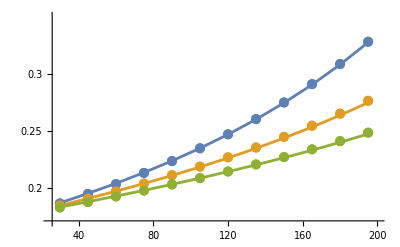

```mathematica
pt=Show[ListPlot[GECResults,PlotStyle->{PointSize[0.018]},PlotRange->{{25,200},{0.17,0.35}},Ticks->{Automatic,{0.2,0.25,0.3}}],ListPlot[HFResults,Joined->True,PlotStyle->{Thickness[0.005]}],ListPlot[GECResults,PlotStyle->{PointSize[0.018]}]]
```

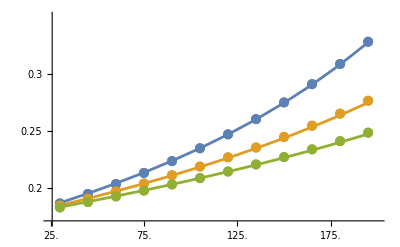

```mathematica
c=3;
tx=Map[MapAt[c #&,#,3]&,Ticks/.AbsoluteOptions[pt,Ticks],{2}];
Show[pt,Ticks->tx]
```

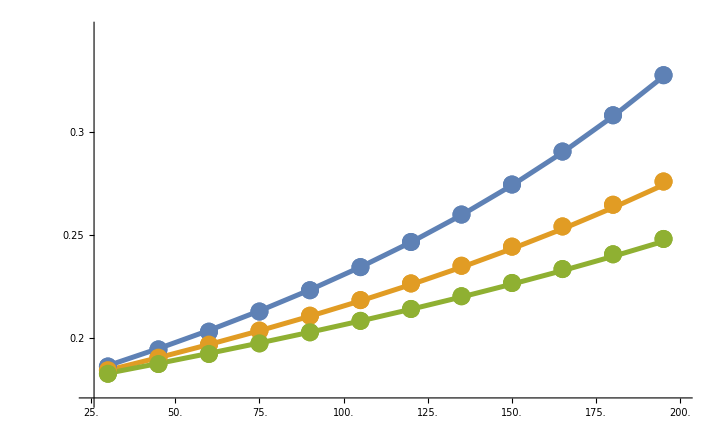

```mathematica
Show[%,PlotLabel->None,LabelStyle->{FontFamily->"cmr10",50,GrayLevel[0]}]
```

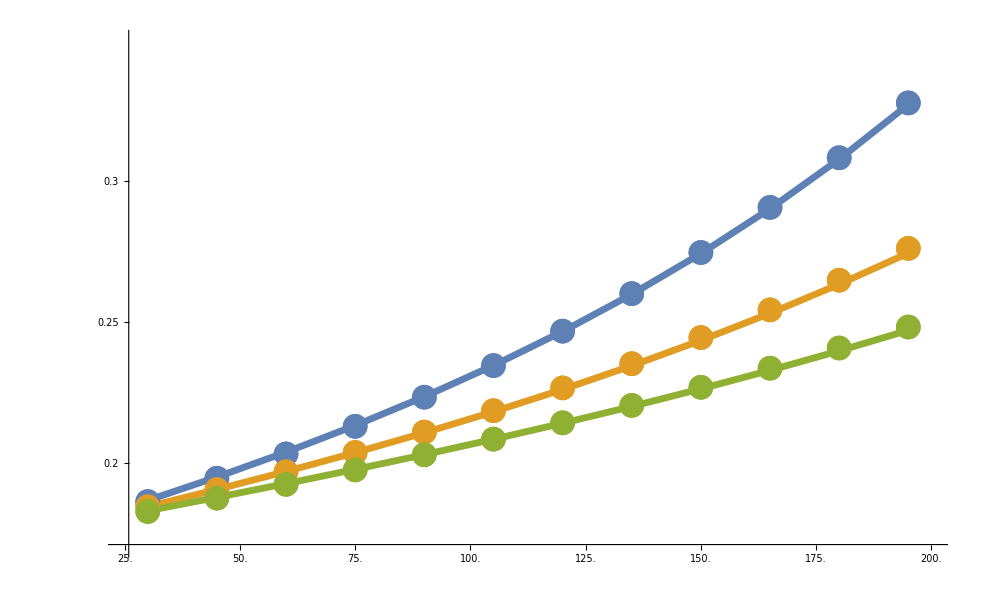

```mathematica
Show[%,AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[3]],Method->{"CoordinatesToolOptions"->{"DisplayFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&),"CopiedValueFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&)}}]
```